Exercises for Section 44 | Importing and Exporting

Import the images from http://google.com. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Import["http://google.com/","Images"]
```

{404. That’s an error.  
The requested URL /images/branding/googlelogo/1x/googlelogo_white_background_color_272x92dp.png was not found on this server. That’s all we know.}

```mathematica
Import["https://www.google.com/?client=safari","Images"]
```

{-Graphics-}

Make an image collage of disks with the dominant colors from images on http://google.com. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ImageCollage@Table[Graphics[{c,Disk[]}],{c,#}]&/@DominantColors[Import["http://google.com/","Images"]]
```

DominantColors::imginv: Expecting an image or graphics instead of {404. That’s an error.  
The requested URL /images/branding/googlelogo/1x/googlelogo_white_background_color_272x92dp.png was not found on this server. That’s all we know.}.

{RGBColor[5.485532947697864*^-6, 5.485532947697871*^-6, 5.485532947697867*^-6],RGBColor[0.9999965522835988, 0.9490162948726993, 0.9490162602773943]}

```mathematica
(*separate here*)
```

```mathematica
ImageCollage@Table[Graphics[{c,Disk[]}],{c,#}]&/@DominantColors[Import["https://www.google.com/?client=safari","Images"]]
```

{-Graphics-}

```mathematica
ImageCollage@
 Flatten[
  Table[Graphics[{c, Disk[]}], {c, #}] & /@ 
   DominantColors[Import["https://www.google.com/", "Images"]], 1]
```

-Graphics-

```mathematica
(*my code works the same. here is ST's ans to complete check*)
ImageCollage[
 Graphics[Style[Disk[], #]] & /@ (Union @@ 
    DominantColors /@ Import["http://google.com", "Images"])]
```

DominantColors::imginv: Expecting an image or graphics instead of {404. That’s an error.  
The requested URL /images/branding/googlelogo/1x/googlelogo_white_background_color_272x92dp.png was not found on this server. That’s all we know.}.

ImageCollage::invimg: Expecting a list of images or graphics instead of {RGBColor[5.485532947697864*^-6, 5.485532947697871*^-6, 5.485532947697867*^-6],RGBColor[0.9999855612679357, 0.9999855612679359, 0.9999855612679357]}.

ImageCollage[{RGBColor[5.485532947697864*^-6, 5.485532947697871*^-6, 5.485532947697867*^-6],RGBColor[0.9999855612679357, 0.9999855612679359, 0.9999855612679357]}]

```mathematica
Rasterize[
 Framed@ImageCollage@
   Flatten[
    Table[Graphics[{c, Disk[]}], {c, #}] & /@ 
     DominantColors[Import["https://www.google.com/", "Images"]], 1], 
 ImageSize -> 350]
```

-Graphics-

Make a word cloud of the text on http://bbc.co.uk. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

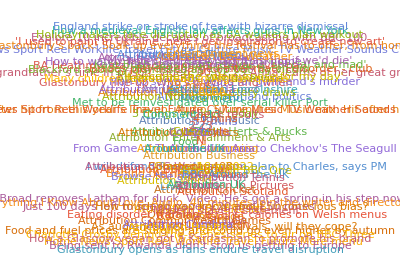

```mathematica
WordCloud[StringSplit[Import["http://bbc.co.uk/"], "\n"]]
```

Make an image collage of the images on http://nps.gov. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ImageCollage@Import["http://nps.gov/", "Images"]
```

Import::htmlimg: Some images could not be imported.

-Graphics-

Use ImageInstanceQ to find pictures on https://en.wikipedia.org/wiki/Ostrich that are of birds. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Select[Import["https://en.wikipedia.org/wiki/Ostrich", "Images"], 
 ImageInstanceQ[#, "ostrich"] &]
```

{-Graphics-,-Graphics-,-Graphics-}

Use TextCases with "Country" to find instances of country names on http://nato.int, and make a word cloud of them. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

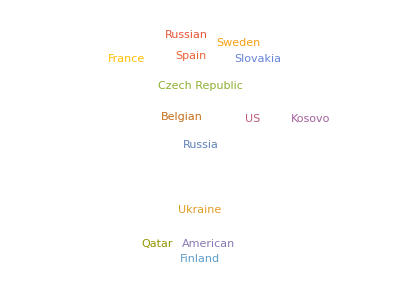

```mathematica
WordCloud@TextCases[Import["http://nato.int/"], "Country"]
```

Find the number of links on https://en.wikipedia.org. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Length@Import["https://en.wikipedia.org/", "Hyperlinks"]
```

313

Send yourself mail with a map of your current location. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
map = GeoGraphics[Here]
SendMail["miles.ackerman1@gmail.com", {"subject", "body", map}]
```

-Graphics-

Failure[PlanRestrictionFailure]

```mathematica
SendMail[GeoGraphics[Here]]
```

Failure[PlanRestrictionFailure]

Send yourself mail with an icon of the current phase of the moon. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
MoonPhase[]
```

0.2552

```mathematica
SendMail[MoonPhase["Icon"]]
```

Failure[PlanRestrictionFailure]

```mathematica
(*the ans it wants*)
SendMail[MoonPhase[Now, "Icon"]]
```

Failure[PlanRestrictionFailure]